## 1.3.2 Наилучшее среднеквадратическое приближение. Частная сумма ряда Фурье.

### Выполнил Ерофеевский Александр

Дано: fun - начальная функция, n - степень аппроксиманта, l - длина отрезка

```mathematica
Clear@fourier
fourier[fun_,n_,l_]:=Integrate[fun,{x,-l,l}]/(2l)+Sum[N[Integrate[fun*Cos[k*Pi*x/l],{x,-l,l}]/l*Cos[k*Pi*x/l]+Integrate[fun*Sin[k*Pi*x/l],{x,-l,l}]/l*Sin[k*Pi*x/l]],{k,1,n}]//FullSimplify
```

Результат

```mathematica
ex=fourier[x^2,10,2Pi];
```

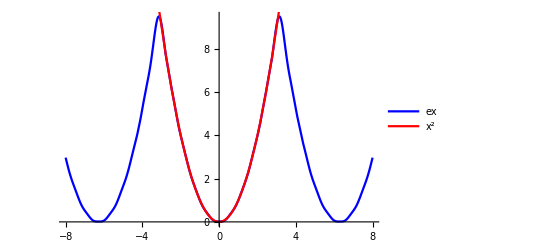

```mathematica
Show[Plot[ex,{x,-8,8},PlotStyle->Blue, PlotLegends->{"ex"}],Plot[x^2,{x,-8,8},PlotStyle->Red,PlotLegends->{"x^2"}]]
```

```mathematica
Clear@f2
f2[x_]:=Sin[x]^2
ex2 = fourier[f2[x],5,Pi];
```

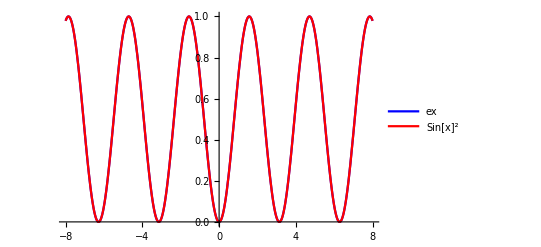

```mathematica
Show[{Plot[ex2,{x,-8,8},PlotStyle->Blue, PlotLegends->{"ex"}],Plot[f2[x],{x,-8,8},PlotStyle->Red,PlotLegends->{"Sin[x]^2"}]}]
```